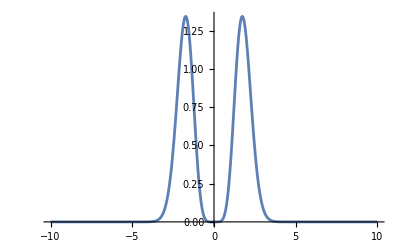

```mathematica
Plot[x^6*Exp[-x^2],{x,-10,10},PlotRange->All](*可積分な優函数がほしい*)
```

```mathematica
Integrate[-Sin[x]*Exp[-t*x],x](*この積分覚えたい*)
```

(ⅇ^(-t x) (Cos[x]+t Sin[x]))/(1+t^2)

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}](*Lebesgue非可測だよ*)
```

π/2

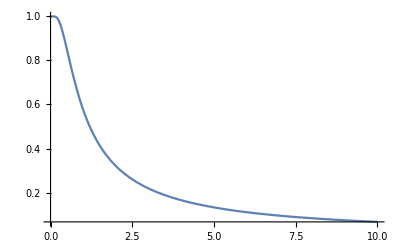

```mathematica
Plot[2Sinh[1/x]/(1+2Cosh[1/x]),{x,0,10},PlotRange->All](*磁化の温度依存やったと思う*)
```

```mathematica
myParitionsP[n_]:=1/(4*n* Sqrt[3])Exp[Pi*Sqrt[2n/3]](*分割数の近似*)
```

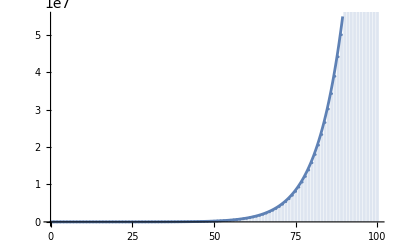

```mathematica
Show[Plot[myParitionsP[n],{n,0,100}],DiscretePlot[PartitionsP[n],{n,0,100}]](*分割数とその近似の比較*)
```

```mathematica
PartitionsQ[4](*同じ数を許さない分割*)
```

2

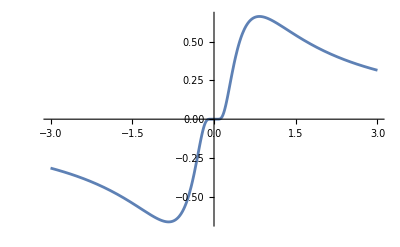

```mathematica
Plot[1/(T Cosh[1/T]),{T,-3,3}](*負の温度を考えたいらしい*)
```

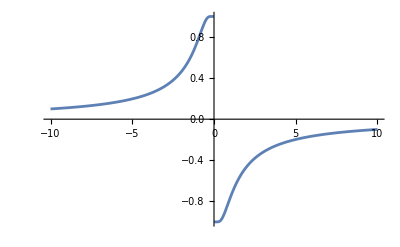

```mathematica
Plot[-Tanh[1/T],{T,-10,10}](*熱容量か内部エネルギーやっけな*)
```

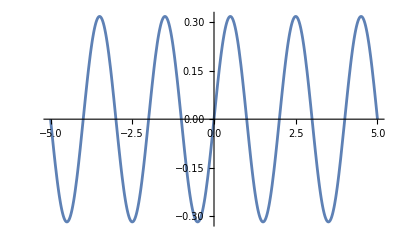

```mathematica
Plot[1/(Gamma[x]Gamma[1-x]),{x,-5,5}](*sinとΓの関係*)
```

```mathematica
Plot[Sin[Pi*x]/Pi,{x,-5,5}]
```

-Graphics-

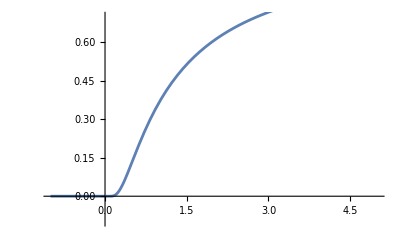

```mathematica
Plot[Exp[-1/x],{x,0.01,5}];
Plot[0,{x,-1,0}];
Show[%%,%,PlotRange->{-0.1,0.7}](*C^∞級だが解析的でない*)
```

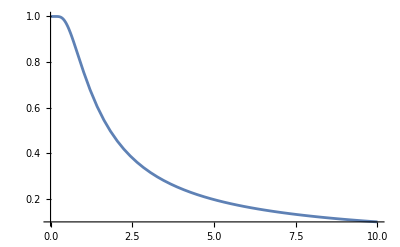

```mathematica
Plot[Tanh[1/x],{x,0,10}]
```

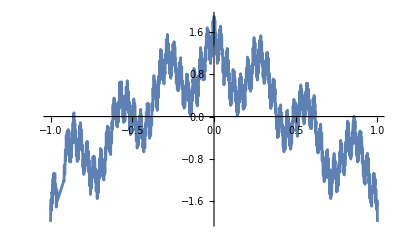

```mathematica
Plot[Sum[2^(-n)Cos[7^n Pi x],{n,0,1000}],{x,-1,1}]
```